# Trichinella DR

```mathematica
SetDirectory["R:\\Projecten\\V092112 Trichinella\\AAA - model\\Model\\Dose Response"];
ab =Import[ "trich-ab.csv"];
```

## Approximated for large n

```mathematica
FullSimplify[Gamma[a+b]/(Gamma[a]Gamma[b])Integrate[ p^(a-1)(1-p)^(b-1)Exp[-r p n], {p,0,1}, Assumptions->{a>0, b>0, n>0}]]
```

Hypergeometric1F1[a,a+b,-n r]

```mathematica
FullSimplify[Gamma[a+b]/(Gamma[a]Gamma[b])Integrate[ p^(a-1)(1-p)^(b-1) (1-p)^(r n) , {p,0,1}, Assumptions->{a>0, b>0, n>0, r>0, r<1}]]
```

(Gamma[a+b] Gamma[b+n r])/(Gamma[b] Gamma[a+b+n r])

## The unapproximated version, unstable for large n

```mathematica
FullSimplify[Gamma[a+b]/(Gamma[a]Gamma[b])Integrate[ p^(a-1)(1-p)^(b-1) (1-r p)^n , {p,0,1}, Assumptions->{a>0, b>0, n>0, r>0, r<1}]]
```

Hypergeometric2F1[a,-n,a+b,r]

## Special case r = 1, the above expressions do not converge in this case!

```mathematica
Integrate[ p^(a-1)(1-p)^(b-1)(1- p)^n, {p,0,1}, Assumptions->{a>0, b>0, n>0}]
```

(Gamma[a] Gamma[b+n])/Gamma[a+b+n]

## An approximation?

```mathematica
res[d_] := Hypergeometric1F1[a,a+b,-r d] -Gamma[a+b]/Gamma[b] Gamma[b+d r]/Gamma[a+b+d r]
```

```mathematica
Mean[ res[100] /.  {r->0.7,  a->abᵀ[[1]],  b->abᵀ[[2]]}]
```

0.000862412

```mathematica
Length[ab]
```

1000

```mathematica
{a,b}/. N[{ a->Take[ abᵀ[[1]],10],  b->Take[abᵀ[[2]],10]},5]
```

{{3.42213,86.2612,0.730107,0.106679,0.00384263,15337.4,1.33253,373.615,0.000459002,0.315415},{24.8637,46.051,166.943,2.26089,3.17529,951.809,9.44298,22872.4,1.22824,17.7014}}

```mathematica
pill[d_,a_,b_,r_]:=If[ d<75, 1+Beta[a,b+d]/Beta[a,b]-Hypergeometric2F1[a,-d,a+b,r]-Hypergeometric2F1[a,-d,a+b,1-r],1+Beta[a,b+d]/Beta[a,b]- Hypergeometric1F1[a,a+b,-d r]-Hypergeometric1F1[a,a+b,-d (1-r)]]
```

```mathematica
pillapprox[d_,a_,b_,r_]:=If[ d<60, 1+Beta[a,b+d]/Beta[a,b]-Hypergeometric2F1[a,-d,a+b,r]-Hypergeometric2F1[a,-d,a+b,1-r],1+Gamma[a+b]/Gamma[b](Gamma[b+d]/Gamma[a+b+d]-Gamma[b+d r]/Gamma[a+b+d r]-Gamma[b+d (1-r)]/Gamma[a+b+d(1-r)])]
```

```mathematica
pill2[d_]:=pill[d, a,b,7/10] /. { a->abᵀ[[1]],  b->abᵀ[[2]]}
```

```mathematica
pill3[d_]:=pillapprox[N[d,5], a,b,0.7] /. { a->abᵀ[[1]],  b->abᵀ[[2]]}
```

```mathematica
ProgressIndicator[Dynamic[d],{1,1000}]
```

```mathematica
t=Table[ {Table[d,{Length[ab]}],pill3[d]}ᵀ, {d,1,1000}];
ListPlot[ tᵀ, Joined->True]
```

-Graphics-

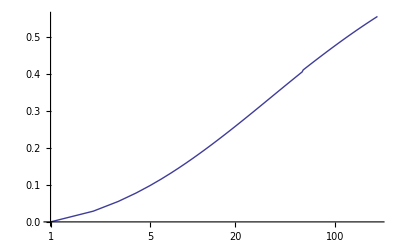

```mathematica
ListLogLinearPlot[ Mean[tᵀ], Joined->True]
```

```mathematica
Export["pill.csv", SetPrecision[Table[t[[i]]ᵀ[[2]],{i,1,200}]ᵀ,2]]
```

pill.csv

## Comparing DR of me and Peter

```mathematica
g[d_,p_,r_]:=(1-(1-p)^d-d p (1-p)^(d-1))(1+(1-p)^d-(1-p r)^d -(1-p(1-r))^d)
f[d_,p_,r_]:=(1+(1-p)^d-(1-p r)^d -(1-p(1-r))^d)
```

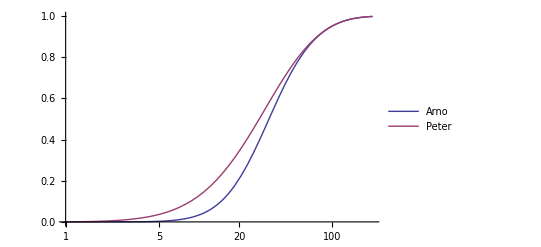

```mathematica
LogLinearPlot[ {g[d,0.1,0.7],f[d,0.1,0.7]}, {d,1,200}, PlotLegends->{"Arno", "Peter"}]
```

```mathematica
pp =Mean[ BetaDistribution[ a,b]]/. { a->abᵀ[[1]],  b->abᵀ[[2]]};
```

```mathematica
ClearAll[d]
```

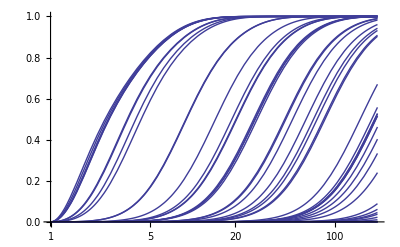

```mathematica
LogLinearPlot[ Thread[ g[d,Take[pp,50],0.7]], {d,1,200}]
```